## Coulomb Potential Inside Heavy Neutral Atoms

***This exercise could be used as an example for the Variational Methods section***

The nonlinear differential equation

ϕ''(x)==(ϕ(x))^(3/2)/(√x),

along with the boundary conditions

ϕ(0)==1,ϕ(∞)==0,

describes the screening of the Coulomb potential inside heavy neutral atoms. However, there is no closed-form solution of equation (DisplayFormulaNumbered).

The Euler–Lagrange equation

(∂ℱ)/(∂ϕ)-ⅆ_x(∂ℱ)/(∂ϕ')==0

applied to the functional

ℱ[ϕ][x]==1/2(ϕ'(x))^2+2/5(ϕ(x))^(5/2)/(√x)

yields the differential equation (DisplayFormulaNumbered).

Show that ϕ_0(x)==144 x^-3 satisfies the differential equation (DisplayFormulaNumbered) for x≥0 and the second boundary condition ϕ(∞)==0. [2 Marks]

Define ϕ_0(x):

```mathematica
Subscript[ϕ, 0](x_)=144/x^3;
```

It satisfies the differential equation (DisplayFormulaNumbered) for x≥0: [1 Mark]

```mathematica
Simplify[ϕ''(x)==(ϕ(x))^(3/2)/(√x)/.ϕ->Subscript[ϕ, 0],x≥0]
```

True

It satisfies the second boundary condition ϕ(∞)==0: [1 Mark]

```mathematica
lim_(x->∞) Subscript[ϕ, 0](x)
```

0

Show that the Euler–Lagrange equation (DisplayFormulaNumbered) applied to functional (DisplayFormulaNumbered) yields the differential equation (DisplayFormulaNumbered). [2 Marks]

Define the functional (DisplayFormulaNumbered): [1 Mark]

```mathematica
ℱ[ϕ_][x_]:=1/2(ϕ'(x))^2+2/5(ϕ(x))^(5/2)/(√x)
```

Show that the Euler–Lagrange equation (DisplayFormulaNumbered) applied to functional (DisplayFormulaNumbered) yields the differential equation (DisplayFormulaNumbered):  [1 Mark]

```mathematica
(∂ℱ[ϕ][x])/(∂ϕ(x))-Subscript[ⅆ, x](∂ℱ[ϕ][x])/(∂ϕ'(x))==0//Simplify
```

ϕ''(x)==(ϕ(x))^(3/2)/(√x)

Consider the two-parameter trial function

ϕ_(α,β)(x)=1/((1+(x/β)^(3/α))^α)

Given that

⟨ℱ_(α,β)⟩=∫_0^∞ ℱ[ϕ_(α,β)][x]==(4 √β α/6+1 (7 α)/3)/(5 (5 α)/2)+(9 2-α/3 (7 α)/3+1)/(14 β 2 α+2)

use FindRoot to obtain the optimal values of α>0 and β>0 by determining the stationary value of ⟨ℱ_(α,β)⟩, and plot the resulting variational solution ϕ_(α,β)(x). [3 Marks]

Define the two-parameter trial function and ⟨ℱ_(α,β)⟩: [1 Mark]

```mathematica
Subscript[ϕ, α_,β_](x_)=1/((1+(x/β)^(3/α))^α);
```

```mathematica
⟨Subscript[ℱ, α_,β_]⟩=(4 √β α/6+1 (7 α)/3)/(5 (5 α)/2)+(9 2-α/3 (7 α)/3+1)/(14 β 2 α+2);
```

Use FindRoot to obtain the optimal values of α>0 and β>0 by determining the stationary value of ⟨ℱ_(α,β)⟩: [1 Mark]

```mathematica
FindRoot[{(∂⟨Subscript[ℱ, α,β]⟩)/(∂α)==0,(∂⟨Subscript[ℱ, α,β]⟩)/(∂β)==0},{α,5},{β,3}]
```

{α→3.36169,β→3.96707}

Plot the resulting variational solution ϕ_(α,β)(x). [1 Mark]

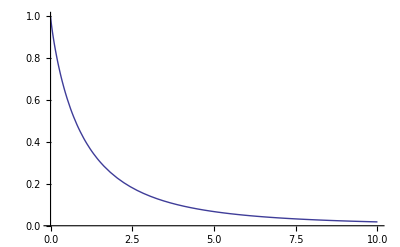

```mathematica
Plot[Evaluate[Subscript[ϕ, α,β](x)/.%],{x,0,10},PlotRange->All]
```